```mathematica
f[z_]:=c/Sqrt[2]*Cosh[z/Sqrt[2]]+2*lambda3
```

```mathematica
Integrate[f[z],{z,-a,a}]
```

```mathematica
4 a lambda3+2 c Sinh[a/(√2)]
Integrate[z^2*f[z],{z,-a,a}]
```

4 a lambda3+2 c Sinh[a/(√2)]

(4 a^3 lambda3)/3-4 √2 a c Cosh[a/(√2)]+2 (4+a^2) c Sinh[a/(√2)]

```mathematica
sys = {x1+x2==1, x2+x3==0}
vars = {x1,x2}
Solve[sys,vars]
```

{x1+x2==1,x2+x3==0}

{x1,x2}

{{x1→1+x3,x2→-x3}}

```mathematica
sys = {1==(4 a^3 lambda3)/3-4 √2 a c Cosh[a/(√2)]+2 (4+a^2) c Sinh[a/(√2)],1==4 a lambda3+2 c Sinh[a/(√2)]}
vars = {a,c}
Solve[sys,vars]
```

{1==(4 a^3 lambda3)/3-4 √2 a c Cosh[a/(√2)]+2 (4+a^2) c Sinh[a/(√2)],1==4 a lambda3+2 c Sinh[a/(√2)]}

{a,c}

```mathematica
Simplify[1/(b-a)*((a^2+b^2)/3-2/3*a*b)/((b-a)^2/12+(b+a)^2/4)]
```

```mathematica
(-a+b)/(a^2+a b+b^2);
Simplify[D[%,{b}]]
```

```mathematica
(2 a^2+2 a b-b^2)/((a^2+a b+b^2)^2);
Roots[%==0,b]
```

b==a-√3 a||b==a+√3 a

```mathematica
f[x_]:=1/2*(lambda1+lambda2 x+lambda3 x^2)
{Integrate[f[x],{x,-a,a}]==1,Integrate[x*f[x],{x,-a,a}]==0,Integrate[x^2*f[x],{x,-a,a}]==1}
Solve[%,{lambda1,lambda2,lambda3}]
fstar[x_]:=Evaluate[1/2*(%[[1]][[1]][[2]] + %[[1]][[3]][[2]]*x^2)]
Simplify[fstar[x]]
Integrate[fstar[x]^2,{x,-a,a}]/.a->1090//N
Integrate[x^2*fstar[x],{x,-a,a}]
(*Roots[D[%,{a}]==0,a]
Simplify[fstar[x]/.a->1]
*)(*Integrate[fstar[x]^2,{x,-a,a}]/.a->Sqrt[5]
(*Plot[Integrate[fstar[x]^2,{x,-a,a}],{a,2,2.5}]*)
Plot[Integrate[1-a^2x^2,{x,-a,a}],{a,2,2.5}]
r:=Roots[3*a^4-10a^2+15==0,a]*)

(*Solve[9 a^4+45 x^2-15 a^2 (1+x^2)==1-x^2,{a}]
%[[1]]*)
```

{a lambda1+(a^3 lambda3)/3==1,(a^3 lambda2)/3==0,(a^3 lambda1)/3+(a^5 lambda3)/5==1}

{{lambda1→(3 (-5+3 a^2))/(4 a^3),lambda2→0,lambda3→-(15 (-3+a^2))/(4 a^5)}}

(9 a^4+45 x^2-15 a^2 (1+x^2))/(8 a^5)

0.00103211

1

```mathematica
f[z_]:=c1*Exp[z]+c2*Exp[-z]+d
{Integrate[f[z],{z,-a,a}]==1,Integrate[z*f[z],{z,-a,a}]==0,Integrate[z^2*f[z],{z,-a,a}]==1}
```

{2 (a d+(c1+c2) Sinh[a])==1,2 (c1-c2) (a Cosh[a]-Sinh[a])==0,(2 a^3 d)/3-4 a (c1+c2) Cosh[a]+2 (2+a^2) (c1+c2) Sinh[a]==1}

```mathematica
Solve[%,{c1,c2,d}]
```

{}

```mathematica
f[z_]:=c*Cosh[z]+d
{Integrate[f[z],{z,-a,a}]==1,Integrate[z^2*f[z],{z,-a,a}]==1}
Solve[%,{c,d}]
%[[1]][[1]][[2]]*Cosh[z]+%[[1]][[2]][[2]]
```

{2 (a d+c Sinh[a])==1,(2 a^3 d)/3-4 a c Cosh[a]+2 (2+a^2) c Sinh[a]==1}

{{c→-(-3+a^2)/(4 (-3 a Cosh[a]+3 Sinh[a]+a^2 Sinh[a])),d→(3 (-2 a Cosh[a]+Sinh[a]+a^2 Sinh[a]))/(4 a (-3 a Cosh[a]+3 Sinh[a]+a^2 Sinh[a]))}}

-((-3+a^2) Cosh[z])/(4 (-3 a Cosh[a]+3 Sinh[a]+a^2 Sinh[a]))+(3 (-2 a Cosh[a]+Sinh[a]+a^2 Sinh[a]))/(4 a (-3 a Cosh[a]+3 Sinh[a]+a^2 Sinh[a]))

```mathematica
pdf[a_,z_]:=-(((-3+a^2) Cosh[z])/(4 (-3 a Cosh[a]+3 Sinh[a]+a^2 Sinh[a])))+(3 (-2 a Cosh[a]+Sinh[a]+a^2 Sinh[a]))/(4 a (-3 a Cosh[a]+3 Sinh[a]+a^2 Sinh[a]))
Integrate[z^2*pdf[a,z],{z,-a,a}]
Integrate[pdf[a,z]^2,{z,-a,a}]
N[%]
```

1

(95-20 ⅇ^2+ⅇ^4)/(4 (-7+ⅇ^2)^2)

3.00108

```mathematica
(95-20 ⅇ^2+ⅇ^4)/(4 (-7+ⅇ^2)^2)
```

(95-20 ⅇ^2+ⅇ^4)/(4 (-7+ⅇ^2)^2)

(95-20 ⅇ^2+ⅇ^4)/(4 (-7+ⅇ^2)^2 N)

```mathematica
a:=5
cdf[a_,w_]:=Integrate[pdf[a,z],{z,-a,w}]
Integrate[w*cdf[a,w]*pdf[a,w],{w,-a,a}]
N[%]
```

(30199-3768 ⅇ^10+2469 ⅇ^20)/(40 (43-13 ⅇ^10)^2)

```mathematica
a:=30
Integrate[pdf[a,z]^2,{z,-a,a}] - Integrate[w*cdf[a,w]*pdf[a,w],{w,-a,a}];
N[%]
```

-1.76888

```mathematica
(*van der vaart's solution to min int f(x)^2. matches that obtained by calc of var.*)
f[x_]:=1-x^2
Integrate[f[x],{x,-a,a}]
ff[x_]:=Evaluate[f[x]/%]
Simplify[Integrate[ff[x],{x,-a,a}]]
sd:=Sqrt[Integrate[x^2*ff[x],{x,-a,a}]]
fff[x_]:=Evaluate[ff[x*sd]*sd]
Simplify[Integrate[x^0*fff[x],{x,-a/sd,a/sd}]]
FullSimplify[fff[x]/.a->1]
(*Integrate[fff[x]^2,{x,-a/sd,a/sd}]
%/.a->1//N
Simplify[ff[x]]
Integrate[fff[x]^2,{x,-a,a}]/.a->1//N*)
```

2 a-(2 a^3)/3

1

1

-(3 (-5+x^2))/(20 √5)

```mathematica
f[z_]:=a*Cosh[z]+b
Integrate[f[z],{z,-ArcCosh[-b/a],ArcCosh[-b/a]}];
ff[z_]:=Evaluate[f[z]/%]
(*Map[Integrate[z^# ff[z],{z,-ArcCosh[-b/a],ArcCosh[-b/a]}]&,{0,1,2}]*)
(*Simplify[ff[z]];*)
sd:=Sqrt[Integrate[z^2*ff[z],{z,-ArcCosh[-b/a],ArcCosh[-b/a]}]]
N[sd*Integrate[ff[z]^2,{z,-ArcCosh[-b/a],ArcCosh[-b/a]}]]
(*fff[z_]:=Evaluate[ff[z*sd]*sd]
*)(*Map[Integrate[z^#*fff[z],{z,-ArcCosh[-b/a]/sd,ArcCosh[-b/a]/sd}],{0}]*)
(*Integrate[z^2*fff[z],{z,-ArcCosh[-b/a]/sd,ArcCosh[-b/a]/sd}]
*)(*mma chockes on simplifying above integration to be var=1, but it checks out for specific values of a and b*)
(*FullSimplify[fff[z]]*)
```

0.269537-1.65044×10^-17 ⅈ

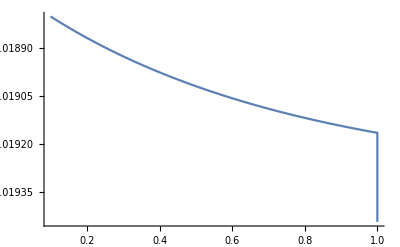

```mathematica
(*like above, recognized a is redundant*)
f[z_]:=-Cosh[z]+b
Integrate[f[z],{z,-ArcCosh[b],ArcCosh[b]}];
ff[z_]:=Evaluate[f[z]/%];
cdf[z_]:=Integrate[ff[w],{w,-ArcCosh[b],z}];
(*Map[Integrate[z^# ff[z],{z,-ArcCosh[b],ArcCosh[b]}]&,{0,1,2}]
*)
Simplify[ff[z]];
sd:=Sqrt[Integrate[z^2*ff[z],{z,-ArcCosh[b],ArcCosh[b]}]]
obj:=FullSimplify[sd*Integrate[ff[z]^2,{z,-ArcCosh[b],ArcCosh[b]}] - Integrate[ff[z]*cdf[z]*z,{z,-ArcCosh[b],ArcCosh[b]}]/sd]
Plot[obj,{b,1,.1}]
(*obj:=FullSimplify[sd*Integrate[ff[z]^2,{z,-ArcCosh[b],ArcCosh[b]}]]
Plot[obj,{b,.1,2}]
*)(*Solve[D[%,b]==0,b]
*)(*Roots[D[b^2-1,b]==0,b]
*)(*fff[z_]:=Evaluate[ff[z*sd]*sd]
*)(*Map[Integrate[z^#*fff[z],{z,-ArcCosh[-b/a]/sd,ArcCosh[-b/a]/sd}],{0}]*)
(*Integrate[z^2*fff[z],{z,-ArcCosh[-b/a]/sd,ArcCosh[-b/a]/sd}]
*)
```

```mathematica
obj/.b->1.2//N
```

-184.461+0. ⅈ

```mathematica
obj/.b->.9//N
```

1145.91+7.01668×10^-14 ⅈ

```mathematica
obj
```

(b (-21 (-1+b^2)+3 (3+4 b^2) ArcCos[b]^2+2 ArcCos[b]^4)+√(-1+b) √(1+b) ArcCosh[b] (3 (5+9 b^2)+2 (3+b^2) ArcCosh[b]^2))/(8 (√(-1+b) √(1+b)-b ArcCosh[b])^3 √((18 √(-1+b) √(1+b)+9 √(-1+b) √(1+b) ArcCosh[b]^2-3 b ArcCosh[b] (6+ArcCosh[b]^2))/(√(-1+b) √(1+b)-b ArcCosh[b])))

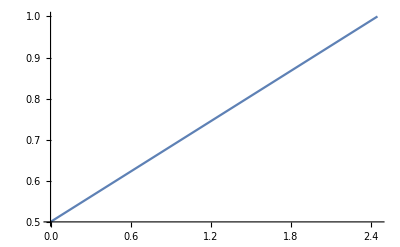

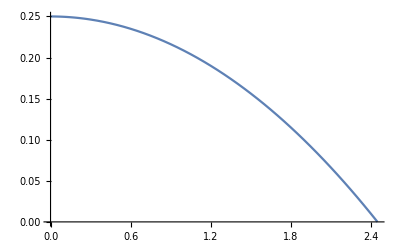

0.408248

1

```mathematica
b:=Sqrt[6];
cdf[s_]:=1/2*(1+s/b)
Plot[cdf[s],{s,0,b}]
Plot[cdf[s]*(1-cdf[s]),{s,0,b}]
Integrate[cdf[s]*(1-cdf[s]),{s,0,b}]//N
Integrate[2*s*(1-cdf[s]),{s,0,b}];
cdf[s_]:=1/2*(1+s/b);
Simplify[Integrate[2*s*(1-cdf[s]),{s,0,b}]]
2*Integrate[cdf[s]*(1-cdf[s]),{s,0,b}]
```

√(2/3)

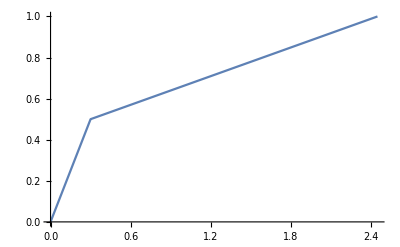

√(2/3)

√(1+1/6 delta (√6+2 delta))

```mathematica
√(2/3)


cdf[s_]:=Piecewise[{{s/2/delta,0≤s≤delta},{1/2+(s-delta)/2/(Sqrt[6]-delta),delta≤s≤Sqrt[6]}}]
Plot[cdf[s]/.delta->.3,{s,0,Sqrt[6]}]
2*Integrate[cdf[s]*(1-cdf[s]),{s,0,Sqrt[6]},Assumptions->0<delta<Sqrt[6]]
FullSimplify[Sqrt[2*Integrate[s*(1-cdf[s]),{s,0,Sqrt[6]},Assumptions->0<delta<Sqrt[6]]]]
```

```mathematica
(*treating endpoints as variable*)
f[z_]:=Cosh[z]+b
Integrate[f[z],{z,-a,a}];
ff[z_]:=Evaluate[f[z]/%];
sd:=Sqrt[Simplify[Integrate[z^2*ff[z],{z,-a,a}]]];
(*fff[z_]:=ff[z*sd]*sd;
Simplify[Integrate[z^2*fff[z],{z,-a/sd,a/sd}]];
FullSimplify[fff[z]];*)
```

```mathematica
Integrate[fff[z]^2,{z,-a/sd,a/sd}]/.{a->-5,b->6}//N
```

```mathematica
-0.6710086168661844
```

```mathematica
f[z_]:=a*Cosh[z]+b
moment0:=Integrate[f[z],{z,-ArcCosh[-b/a],ArcCosh[-b/a]}];
moment2:=Integrate[z^2*f[z],{z,-ArcCosh[-b/a],ArcCosh[-b/a]}]
sys:={moment0==1,moment2==1}
FullSimplify[sys]
Assuming[{{a,b}∈Reals,a<0,b>-a},FindRoot[moment2-1==0,{a,-10}]]
(*Assuming[{{a,b}∈Reals,a<0,b>-a},NSolve[sys,{a,b}]]*);
(*FullSimplify[moment2]*)
```

{2 b ArcCosh[-b/a]==1+(2 (a+b))/(√(1+(2 a)/(-a+b))),4 b ArcCosh[-b/a]+2/3 b ArcCosh[-b/a]^3+2 (a-b) √((a+b)/(-a+b)) (2+ArcCosh[-b/a]^2)==1}

FindRoot::nlnum: The function value {-1.+0.666667 b Log[0.1 (b+Power[«2»])]^3+(4. (100.-1. b Plus[«2»])+4. b (b+√Plus[«2»]) Log[0.1 Plus[«2»]]+2. (100.-1. b Plus[«2»]) Log[Times[«2»]]^2)/(b+√(-100.+Power[«2»]))} is not a list of numbers with dimensions {1} at {a} = {-10.}.

FindRoot::nlnum: The function value {-1.+4. b ArcCosh[0.1 b]+0.666667 b ArcCosh[0.1 b]^3+2. (-10.-1. b) √((-10.+b)/(10.+b)) (2.+ArcCosh[0.1 b]^2)} is not a list of numbers with dimensions {1} at {a} = {-10.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot[moment2-1==0,{a,-10}]

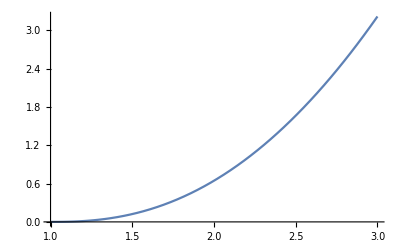

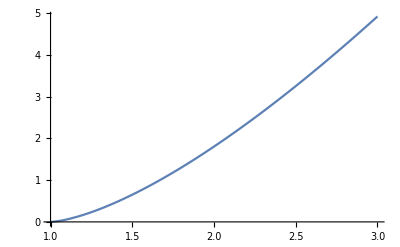

```mathematica
Plot[moment2/.a->-1,{b,1,3}]
Plot[moment0/.a->-1,{b,1,3}]
```

```mathematica
ArcCosh[-b/a]^3/.b->-10/.a->1//N
```

26.8174

```mathematica
f[z_]:=a*Cosh[z]+b
moment0:=Integrate[f[z],{z,-ArcCosh[-b/a],ArcCosh[-b/a]}];
moment2:=Integrate[z^2*f[z],{z,-ArcCosh[-b/a],ArcCosh[-b/a]}]
sys:={moment0==1,moment2==1}
FullSimplify[sys]
```

{2 b ArcCosh[-b/a]==1+(2 (a+b))/(√(1+(2 a)/(-a+b))),4 b ArcCosh[-b/a]+2/3 b ArcCosh[-b/a]^3+2 (a-b) √((a+b)/(-a+b)) (2+ArcCosh[-b/a]^2)==1}

```mathematica
u:=(1+(2 (a+b))/(√(1+(2 a)/(-a+b))))/(2b)
Simplify[4 b u+2/3 b u^3+2 (a-b) √((a+b)/(-a+b)) (2+u^2)]
Assuming[{{a,b}∈Reals,a<0,b>-a},Solve[%==0,{b}]]
```

1+(8 a^2 √((a+b)/(-a+b)))/(3 (a+b))-(4 b^2 √((a+b)/(-a+b)))/(3 (a+b))+(1/12+a^2-(4 a^4 √((a+b)/(-a+b)))/(3 (a+b)))/b^2

{{b→Root[-1-24 a^2-144 a^4-256 a^6+(-24-288 a^2+768 a^4) #1^2+(-144-768 a^2) #1^4+256 #1^6&,2]}}

```mathematica
Assuming[{{a,b}∈Reals,a<0,b>-a},Solve[2 b ArcCosh[-b/a]==1+(2 (a+b))/(√(1+(2 a)/(-a+b)))/.a->-1,{b}]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[2 b ArcCosh[b]==1+(2 (-1+b))/(√(1-2/(1+b))),{b}]

```mathematica
f[z_]:=a*Cosh[z]+b
moment0:=Integrate[f[z],{z,-ArcCosh[-b/a],ArcCosh[-b/a]}];
moment2:=Integrate[z^2*f[z],{z,-ArcCosh[-b/a],ArcCosh[-b/a]}]
(*sys:={moment0==1,moment2==1}
FullSimplify[sys]*)
obj[a_,b_]:=Evaluate[Abs[moment0-1]^1+Abs[moment2-1]^1]
Plot3D[obj[a,b],{a,-10,-1},{b,-a,-a+3},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*power law example*)
c:=((p+1)/2)^(1/(p+1))
sigma:=Sqrt[2/(p+3)*c^(p+3)];
f[z_]:=Abs[z]^p*sigma^(p+1);
(*Assuming[p>-1,Integrate[z^2*f[z],{z,-c/sigma,c/sigma}]]*)
(*Assuming[p>-1,Integrate[f[z]^2,{z,-c/sigma,c/sigma}]]*)
cdf0[z_]:=Integrate[f[w],{w,0,z}]
Assuming[1>p>-1/2  && 0<z<c/sigma,Simplify[cdf0[z]]]
cdf[z_]:=%
cdf[z]
Assuming[1>p>-1/2,Integrate[z*(1-cdf[Abs[z]])*f[z],{z,-c/sigma,0}]] + Assuming[1>p>-1/2,Integrate[z*cdf[z]*f[z],{z,0,c/sigma}]]
(*Assuming[1>p>-1/2,Simplify[%]]
*)(*Assuming[1>p>-1/2,Integrate[z*cdf[z]*f[z],{z,-c/sigma,c/sigma}]]*)
```

1/2 ((1+p)/(3+p))^((1+p)/2) z^(1+p)

1/2 ((1+p)/(3+p))^((1+p)/2) z^(1+p)

(√((1+p) (3+p)))/(12+8 p)-(√((1+p) (3+p)) (6+4 p+(-1)^p (2+p)))/(4 (2+p) (3+2 p))

```mathematica
FullSimplify[%]
```

-(√((1+p) (3+p)) (4+3 p+(-1)^p (2+p)))/(4 (2+p) (3+2 p))

```mathematica
%/.p->0
```

(-5/48+ⅈ/16) √5

```mathematica
Assuming[1>p>-1/2,Integrate[cdf[z]*(1-cdf[z]),{z,0,c/sigma}]]+Assuming[1>p>-1/2,Integrate[cdf[z]*(1-cdf[z]),{z,-c/sigma,0}]]
```

((3+p) (4+3 p))/(4 (2+p) √((1+p) (3+p)) (3+2 p))-((3+p) (ⅇ^(2 ⅈ p π) (2+p)+2 (-1)^p (3+2 p)))/(4 (2+p) √((1+p) (3+p)) (3+2 p))

```mathematica
FullSimplify[%]
```

-((3+p) (-4-3 p+ⅇ^(2 ⅈ p π) (2+p)+2 (-1)^p (3+2 p)))/(4 (2+p) √((1+p) (3+p)) (3+2 p))

```mathematica
FullSimplify[f[z]]
```

2^((1+p)/2) (((2^(-1/(1+p)) (1+p)^(1/(1+p)))^(3+p))/(3+p))^((1+p)/2) Abs[z]^p

```mathematica
pdf[z_]:=Evaluate[%/.p->-1/2]
```

```mathematica
Integrate[1/(4 5^(1/4) √Abs[w]),{w,-Sqrt[5],z}]
```

$Aborted

```mathematica
pdf[z]
```

1/(4 5^(1/4) √Abs[z])

```mathematica
-c/sigma/.p->-1/2
```

-√5

```mathematica
const:=((p+1)/2)^(1/(p+1))
c:=const
sigma:=Sqrt[2/(p+3)*c^(p+3)];
Simplify[const^(p+2)/sigma/(p+1)*(1/2*(p+1)/(p+2)+const^(p+1)/(p+2)/(2*p+3))]
TeXForm[%]
%/.p->-1/2
```

2^(-1/2+1/(1+p)) (1+p)^(-(2+p)/(1+p)) √(((2^(-1/(1+p)) (1+p)^(1/(1+p)))^(3+p))/(3+p)) (3+p) (((2^(-1/(1+p)) (1+p)^(1/(1+p)))^(1+p))/((2+p) (3+2 p))+(1+p)/(4+2 p))

(√5)/8

2^{\frac{1}{p+1}-\frac{1}{2}} (p+1)^{-\frac{p+2}{p+1}} \sqrt{\frac{\left(2^{-\frac{1}{p+1}}
   (p+1)^{\frac{1}{p+1}}\right)^{p+3}}{p+3}} (p+3) \left(\frac{\left(2^{-\frac{1}{p+1}}
   (p+1)^{\frac{1}{p+1}}\right)^{p+1}}{(p+2) (2 p+3)}+\frac{p+1}{2 p+4}\right)

```mathematica
2^(-1/2+1/(1+p)) (1+p)^(-(2+p)/(1+p)) √(((2^(-1/(1+p)) (1+p)^(1/(1+p)))^(3+p))/(3+p)) (3+p) (((2^(-1/(1+p)) (1+p)^(1/(1+p)))^(1+p))/((2+p) (3+2 p))+(1+p)/(4+2 p))
```

```mathematica
%/.p->-1/2
```

(√5)/8

```mathematica
ClearAll["Global`*"]
Simplify[const^(p+2)/sigma/(p+1)*(1/2*(p+1)/(p+2)+const^(p+1)/(p+2)/(2*p+3))]
```

(const^(2+p) (3+2 const^(1+p)+5 p+2 p^2))/(2 (1+p) (2+p) (3+2 p) sigma)

```mathematica
f[z_]:=a Cosh[z/Sqrt[2]]+b
Integrate[f[z],{z,-d,d}]
Integrate[z^2*f[z],{z,-d,d}]
cdf[z_]:=Evaluate[Integrate[f[w],{w,-d,z}]];
Integrate[f[z]^2,{z,-d,d}] - 1/2*Integrate[cdf[z]*(1-cdf[z]),{z,-d,d}]//Simplify;
```

2 (b d+√2 a Sinh[d/(√2)])

(2 b d^3)/3-8 a d Cosh[d/(√2)]+2 √2 a (4+d^2) Sinh[d/(√2)]

```mathematica
(*constraining d=-b/a*)
f[z_]:=a Cosh[z/Sqrt[2]]+b
Integrate[f[z],{z,b/a,-b/a}]
Integrate[z^2*f[z],{z,b/a,-b/a}]
cdf[z_]:=Evaluate[Integrate[f[w],{w,b/a,z}]];
```

-(2 (b^2+√2 a^2 Sinh[b/(√2 a)]))/a

8 b Cosh[b/(√2 a)]-(2 (b^4+3 √2 a^2 (4 a^2+b^2) Sinh[b/(√2 a)]))/(3 a^3)